Importamos los datos

```mathematica
ventosa1 = Import["..\\Data\\VENTOSALIMPIO_.csv"];
rumorosa1 = Import["..\\Data\\RUMOROSALIMPIO_.csv"]; 
ojuelos1 = Import["..\\Data\\OJUELOSLIMPIO_.csv"];
tepexi1 = Import["..\\Data\\TEPEXILIMPIO_.csv"];
sanfer1 = Import["..\\Data\\SANFERNANDOLIMPIO_.csv"];
cuau1 = Import["..\\Data\\CUAHUTEMOCLIMPIO_.csv"];
{{merida1 = Import["..\\Data\\MERIDALIMPIO_.csv"];}, {□}}
```

```mathematica
Length[ventosa1]
Length[rumorosa1]
Length[sanfer1]
Length[cuau1]
Length[merida1]
Length[tepexi1]
Length[ojuelos1]
```

52369

49328

52522

52490

48058

52463

51070

Calculamos la potencia del sitio en general

```mathematica
potenciaventosa = ventosa1[All, 0.6125*ventosa1[[2]]*ventosa1[[2]]*ventosa1[[2]]];
potenciarumorosa = rumorosa1[All, 0.6125*rumorosa1[[2]]*rumorosa1[[2]]*rumorosa1[[2]]];
potenciamerida = merida1[All, 0.6125*merida1[[2]]*merida1[[2]]*merida1[[2]]];
potenciaojuelos = ojuelos1[All, 0.6125*ojuelos1[[2]]*ojuelos1[[2]]*ojuelos1[[2]]];
potenciatepexi = tepexi1[All, 0.6125*tepexi1[[2]]*tepexi1[[2]]*tepexi1[[2]]];
potenciasanfer = sanfer1[All, 0.6125*sanfer1[[2]]*sanfer1[[2]]*sanfer1[[2]]];
potenciacuau = cuau1[All, 0.6125*cuau1[[2]]*cuau1[[2]]*cuau1[[2]]];
```

Calculamos los vectores de viento de los sitios.

```mathematica
merida=Table[merida1[[i,2]]{-Sin[merida1[[i,3]]Degree],Cos[merida1[[i,3]]Degree]},{i,2,Length[merida1]}];
sanfer = Table[sanfer1[[i,2]]{-Sin[sanfer1[[i,3]]Degree],Cos[sanfer1[[i,3]]Degree]},{i,2,Length[sanfer1]}];
cuau = Table[cuau1[[i,2]]{-Sin[cuau1[[i,3]]Degree],Cos[cuau1[[i,3]]Degree]},{i,2,Length[cuau1]}];
tepexi = Table[tepexi1[[i,2]]{-Sin[tepexi1[[i,3]]Degree],Cos[tepexi1[[i,3]]Degree]},{i,2,Length[tepexi1]}];
ojuelos = Table[ojuelos1[[i,2]]{-Sin[ojuelos1[[i,3]]Degree],Cos[ojuelos1[[i,3]]Degree]},{i,2,Length[ojuelos1]}];
rumorosa = Table[rumorosa1[[i,2]]{-Sin[rumorosa1[[i,3]]Degree],Cos[rumorosa1[[i,3]]Degree]},{i,2,Length[rumorosa1]}];
```

La Rumorosa

```mathematica
plotrumorosa = ListPlot[rumorosa, AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, GridLines->{{0},{0}}, ColorFunction->LightPurple]
```

-Graphics-

```mathematica
Histogram3D[rumorosa,60,AxesOrigin->{-15,-20},AxesLabel->{"Vx [m/s]","Vy [m/s]"}, ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
SmoothHistogram3D[rumorosa,ColorFunction->"TemperatureMap",AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, PlotLegends->Automatic]
```

-Graphics3D-

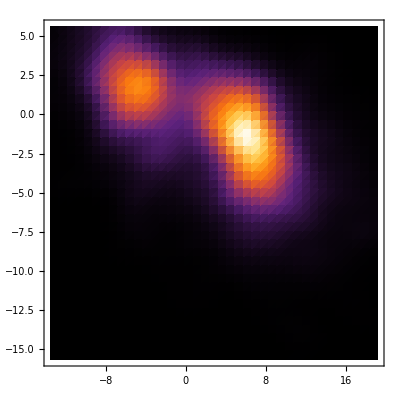

```mathematica
SmoothDensityHistogram[rumorosa,ColorFunction->"SunsetColors"]
```

Encontramos los estados de viento.

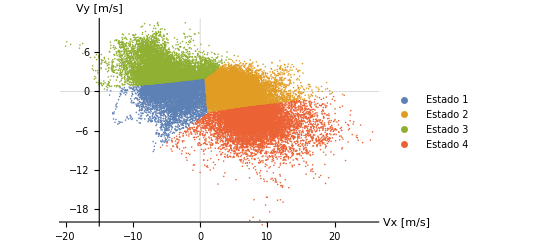

```mathematica
fcrumorosa = FindClusters[rumorosa,4,Method -> "KMeans" ,CriterionFunction->"CalinskiHarabasz"];
ListPlot[fcrumorosa, PlotLegends->{"Estado 1", "Estado 2","Estado 3","Estado 4"},AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, GridLines->{{0},{0}}]
```

Estado de viento 1

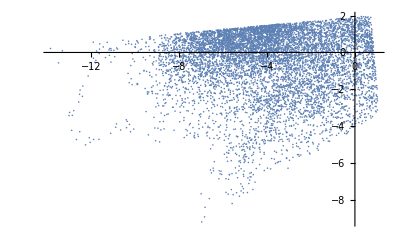

```mathematica
ListPlot[fcrumorosa[[1]]]
```

```mathematica
rumest1 = fcrumorosa[[1]];
rumest2 = fcrumorosa[[2]];
rumest3 = fcrumorosa[[3]];
rumest4 = fcrumorosa[[4]];
```

```mathematica
Length[rumest1]
Length[rumest2]
Length[rumest3]
Length[rumest4]
```

7921

19071

10148

12187

Posteriormente procedemos a formar la cadena de markov y visualizarla. 
Primeramente formamos un arreglo llamado “arrrumorosa” en donde se guarda el estado de viento al que pertenece cada uno de los vectores de velocidad. Recordemos que consideramos una clasificación en cuatro estados de viento, tal información quedó guardada en fcrumorosa.
Posterior a ello, construimos una tabla que contendrá el estado al que pertenece cada uno de los vectores de la serie temporal. Finalmente graficamos esa tabla usando ListLinePlot.

```mathematica
arrrumorosa=ParallelTable[Count[fcrumorosa[[#]],rumorosa[[j]]]&/@{1,2,3,4},{j,1,Length[rumorosa]}];
```

```mathematica
markovrumorosa=Table[Complement[{1,2,3,4},Flatten[Position[arrrumorosa[[j]],0],1]][[1]],{j,1,Length[arrrumorosa]}];
```

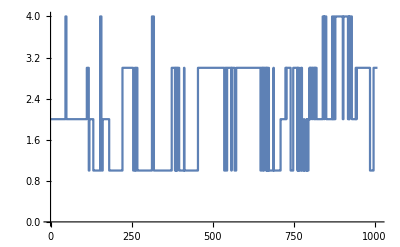

```mathematica
ListLinePlot[markovrumorosa,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

Utilizando los datos de la cadena de markov procedemos a calcular la matriz de transición. En la variable “estadosrumorosa” guardamos el número de estado al que pertenece cada uno de los vectores de la serie temporal. 
En la variable “transrumorosa” construimos una tabla que contiene tuples de dos elementos. El primer elemento representa el estado inmediatamente anterior, el segundo elemento representa el estado actual, de esta forma podemos analizar la transición entre estados. 
Finalmente, en la variable “Matrumorosa” construimos la matriz de transición.

```mathematica
estadosrumorosa= markovrumorosa

transrumorosa = Table[{estadosrumorosa[[i]],estadosrumorosa[[i+1]]},{i,1,Length[estadosrumorosa]-1}]
Probrumorosa[i_,j_]:=Length[Select[transrumorosa,#=={i,j}&]]/Length[Select[transrumorosa,#[[1]]==i&]] 
Matrumorosa=Table[Probrumorosa[i,j],{i,1,4},{j,1,4}] // MatrixForm
Matrumorosa = Table[Probrumorosa[i,j],{i,1,4},{j,1,4}] // MatrixForm // N
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,1,3,3,3,1,3,3,3,3,3,1,1,3,3,3,1,1,3,1,3,1,3,3,1,3,3,3,1,3,3,3,3,3,3,3,3,1,1,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,49003,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,2,4,2,4,4,4,4,4,2,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
 |  |  |  |

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,2},{2,2},{2,2},{2,2},{2,2},{2,3},{3,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},49220,{4,4},{4,2},{2,4},{4,2},{2,4},{4,2},{2,4},{4,4},{4,4},{4,4},{4,4},{4,2},{2,1},{1,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,1},{1,1},{1,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3}}
 |  |  |  |

(6977/7921 | 164/7921 | 726/7921 | 54/7921
191/19071 | 455/489 | 158/19071 | 977/19071
711/10147 | 172/10147 | 9263/10147 | 1/10147
41/12187 | 990/12187 | 1/12187 | 11155/12187)

(0.880823 | 0.0207045 | 0.0916551 | 0.00681732
0.0100152 | 0.93047 | 0.00828483 | 0.0512296
0.07007 | 0.0169508 | 0.912881 | 0.0000985513
0.00336424 | 0.0812341 | 0.0000820546 | 0.91532)

```mathematica
Export["estadosrumorosacompleto.csv",estadosrumorosa,"CSV"]
```

Se obtiene la potencia de cada uno de los estados de viento

```mathematica
potenciarumorosa1 = Total[0.6125(((fcrumorosa[[1]][[All,1]]^2+fcrumorosa[[1]][[All,2]]^2)^(1/2))^3)]/Length[fcrumorosa[[1]]]
potenciarumorosa2 = Total[0.6125(((fcrumorosa[[2]][[All,1]]^2+fcrumorosa[[2]][[All,2]]^2)^(1/2))^3)]/Length[fcrumorosa[[2]]]
potenciarumorosa3 = Total[0.6125(((fcrumorosa[[3]][[All,1]]^2+fcrumorosa[[3]][[All,2]]^2)^(1/2))^3)]/Length[fcrumorosa[[3]]]
potenciarumorosa4 = Total[0.6125(((fcrumorosa[[4]][[All,1]]^2+fcrumorosa[[4]][[All,2]]^2)^(1/2))^3)]/Length[fcrumorosa[[4]]]
```

95.8449

184.29

285.234

748.691

Mérida

```mathematica
plotmerida = ListPlot[merida]
```

```mathematica
Histogram3D[merida,25]
```

```mathematica
SmoothHistogram3D[merida]
```

```mathematica
SmoothDensityHistogram[merida,ColorFunction->"SunsetColors"]
```

```mathematica
fcmerida = FindClusters[merida,4,CriterionFunction->"CalinskiHarabasz"];
```

```mathematica
ListPlot[fcmerida]
```

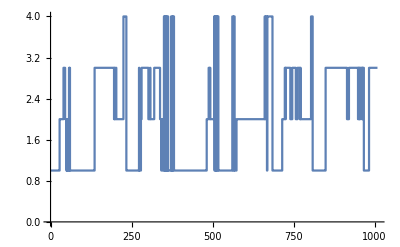

```mathematica
arrmerida=ParallelTable[Count[fcmerida[[#]],merida[[j]]]&/@{1,2,3,4},{j,1,Length[merida]}];
markovmerida=Table[Complement[{1,2,3,4},Flatten[Position[arrmerida[[j]],0],1]][[1]],{j,1,Length[arrmerida]}];
ListLinePlot[markovmerida,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

```mathematica
estadosmerida=markovmerida;

transmerida= Table[{estadosmerida[[i]],estadosmerida[[i+1]]},{i,1,Length[estadosmerida]-1}]
Probmerida[i_,j_]:=Length[Select[transmerida,#=={i,j}&]]/Length[Select[transmerida,#[[1]]==i&]] 
Matmerida=Table[Probmerida[i,j],{i,1,4},{j,1,4}]//MatrixForm
Matmerida=Table[Probmerida[i,j],{i,1,4},{j,1,4}]//MatrixForm // N
```

{{1,1},{1,1},{1,1},{1,1},{1,2},{2,1},{1,1},{1,1},{1,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,1},{1,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,3},{3,2},{2,2},{2,3},{3,2},{2,3},{3,2},{2,2},{2,2},{2,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,2},{2,2},{2,1},{1,1},{1,1},{1,1},47950,{2,2},{2,2},{2,3},{3,3},{3,3},{3,3},{3,2},{2,2},{2,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3}}
 |  |  |  |

(14001/14962 | 162/7481 | 305/14962 | 166/7481
371/12070 | 302/355 | 633/6035 | 33/2414
98/7927 | 686/7927 | 7142/7927 | 1/7927
393/5170 | 53/2585 | 0 | 4671/5170)

(0.935771 | 0.0216549 | 0.020385 | 0.0221895
0.0307374 | 0.850704 | 0.104888 | 0.0136703
0.0123628 | 0.0865397 | 0.900971 | 0.000126151
0.0760155 | 0.0205029 | 0. | 0.903482)

```mathematica
Export["estadosmeridacompleto.csv",estadosmerida,"CSV"]
```

```mathematica
potenciamerida1 = Total[0.6125(((fcmerida[[1]][[All,1]]^2+fcmerida[[1]][[All,2]]^2)^(1/2))^3)]/Length[fcmerida[[1]]]
potenciamerida2 = Total[0.6125(((fcmerida[[2]][[All,1]]^2+fcmerida[[2]][[All,2]]^2)^(1/2))^3)]/Length[fcmerida[[2]]]
potenciamerida3 = Total[0.6125(((fcmerida[[3]][[All,1]]^2+fcmerida[[3]][[All,2]]^2)^(1/2))^3)]/Length[fcmerida[[3]]]
potenciamerida4 = Total[0.6125(((fcmerida[[4]][[All,1]]^2+fcmerida[[4]][[All,2]]^2)^(1/2))^3)]/Length[fcmerida[[4]]]
```

249.503

95.4242

202.775

192.271

Ojuelos

```mathematica
plotojuelos = ListPlot[ojuelos]
```

```mathematica
Histogram3D[ojuelos,25]
```

```mathematica
SmoothHistogram3D[ojuelos]
```

```mathematica
SmoothDensityHistogram[ojuelos,ColorFunction->"SunsetColors"]
```

```mathematica
fcojuelos=FindClusters[ojuelos,4,CriterionFunction->"CalinskiHarabasz"];
```

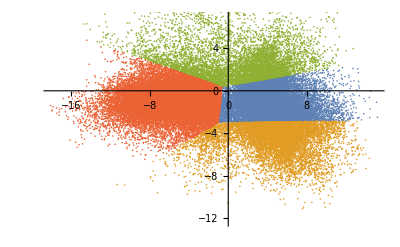

```mathematica
ListPlot[fcojuelos]
```

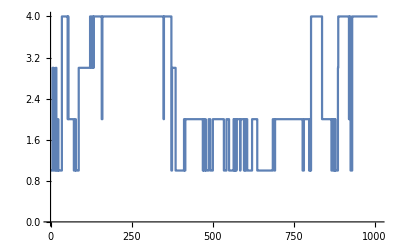

```mathematica
arrojuelos=ParallelTable[Count[fcojuelos[[#]],ojuelos[[j]]]&/@{1,2,3,4},{j,1,Length[ojuelos]}];
markovojuelos=Table[Complement[{1,2,3,4},Flatten[Position[arrojuelos[[j]],0],1]][[1]],{j,1,Length[arrojuelos]}];
ListLinePlot[markovojuelos,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

```mathematica
estadosojuelos= markovojuelos;

transojuelos= Table[{estadosojuelos[[i]],estadosojuelos[[i+1]]},{i,1,Length[estadosojuelos]-1}];
Probojuelos[i_,j_]:=Length[Select[transojuelos,#=={i,j}&]]/Length[Select[transojuelos,#[[1]]==i&]] 
Matojuelos=Table[Probojuelos[i,j],{i,1,4},{j,1,4}]//MatrixForm
Matojuelos=Table[Probojuelos[i,j],{i,1,4},{j,1,4}]//MatrixForm // N
```

(1181/1413 | 1135/12717 | 706/12717 | 247/12717
149/1110 | 1873/2220 | 11/8880 | 1/48
607/6946 | 11/6946 | 2798/3473 | 366/3473
288/22525 | 242/22525 | 634/22525 | 21361/22525)

(0.83581 | 0.0892506 | 0.0555162 | 0.0194228
0.134234 | 0.843694 | 0.00123874 | 0.0208333
0.0873884 | 0.00158365 | 0.805644 | 0.105384
0.0127858 | 0.0107436 | 0.0281465 | 0.948324)

```mathematica
Export["estadosojueloscompleto.csv",estadosojuelos,"CSV"]
```

```mathematica
potenciaojuelos1 = Total[0.6125(((fcojuelos[[1]][[All,1]]^2+fcojuelos[[1]][[All,2]]^2)^(1/2))^3)]/Length[fcojuelos[[1]]]
potenciaojuelos2 = Total[0.6125(((fcojuelos[[2]][[All,1]]^2+fcojuelos[[2]][[All,2]]^2)^(1/2))^3)]/Length[fcojuelos[[2]]]
potenciaojuelos3 = Total[0.6125(((fcojuelos[[3]][[All,1]]^2+fcojuelos[[3]][[All,2]]^2)^(1/2))^3)]/Length[fcojuelos[[3]]]
potenciaojuelos4 = Total[0.6125(((fcojuelos[[4]][[All,1]]^2+fcojuelos[[4]][[All,2]]^2)^(1/2))^3)]/Length[fcojuelos[[4]]]
```

127.337

298.003

140.569

243.316

Cuahutemoc

```mathematica
plotcua = ListPlot[cuau]
```

```mathematica
Histogram3D[cuau,25]
```

```mathematica
cuau3D = SmoothHistogram3D[cuau]
```

```mathematica
SmoothDensityHistogram[cuau,ColorFunction->"SunsetColors"]
```

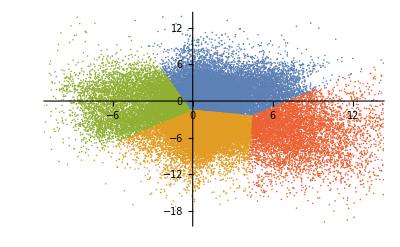

```mathematica
fccuau = FindClusters[cuau,4,Method -> "KMeans" ,CriterionFunction->"CalinskiHarabasz"];
ListPlot[fccuau]
```

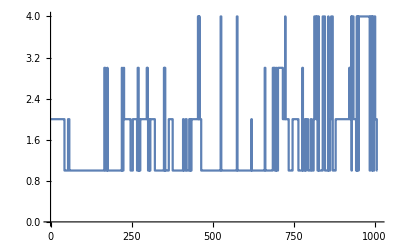

```mathematica
arrcuau=ParallelTable[Count[fccuau[[#]],cuau[[j]]]&/@{1,2,3,4},{j,1,Length[cuau]}];
markovcuau=Table[Complement[{1,2,3,4},Flatten[Position[arrcuau[[j]],0],1]][[1]],{j,1,Length[arrcuau]}];
ListLinePlot[markovcuau,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

```mathematica
estadoscuau= markovcuau;

transcuau= Table[{estadoscuau[[i]],estadoscuau[[i+1]]},{i,1,Length[estadoscuau]-1}]
Probcuau[i_,j_]:=Length[Select[transcuau,#=={i,j}&]]/Length[Select[transcuau,#[[1]]==i&]] 
Matcuau=Table[Probcuau[i,j],{i,1,4},{j,1,4}]//MatrixForm
Matcuau=Table[Probcuau[i,j],{i,1,4},{j,1,4}]//MatrixForm // N
```

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,3},{3,2},{2,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},52382,{4,4},{4,4},{4,4},{4,4},{4,2},{2,2},{2,2},{2,4},{4,2},{2,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,2},{2,2},{2,2},{2,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,1},{1,2},{2,2},{2,2},{2,2},{2,2},{2,2}}
 |  |  |  |

```mathematica
Export["estadoscuauhtemoccompleto.csv",estadoscuau,"CSV"]
```

(18996/21011 | 686/21011 | 1012/21011 | 317/21011
763/15483 | 4596/5161 | 497/15483 | 145/5161
445/4671 | 310/4671 | 7831/9342 | 1/9342
361/6652 | 195/3326 | 1/3326 | 5899/6652)

(0.904098 | 0.0326496 | 0.0481652 | 0.0150873
0.0492799 | 0.890525 | 0.0320997 | 0.0280953
0.0952687 | 0.0663669 | 0.838257 | 0.000107043
0.0542694 | 0.058629 | 0.000300661 | 0.886801)

```mathematica
potenciacuau1 = Total[0.6125(((fccuau[[1]][[All,1]]^2+fccuau[[1]][[All,2]]^2)^(1/2))^3)]/Length[fccuau[[1]]]
potenciacuau2 = Total[0.6125(((fccuau[[2]][[All,1]]^2+fccuau[[2]][[All,2]]^2)^(1/2))^3)]/Length[fccuau[[2]]]
potenciacuau3 = Total[0.6125(((fccuau[[3]][[All,1]]^2+fccuau[[3]][[All,2]]^2)^(1/2))^3)]/Length[fccuau[[3]]]
potenciacuau4 = Total[0.6125(((fccuau[[4]][[All,1]]^2+fccuau[[4]][[All,2]]^2)^(1/2))^3)]/Length[fccuau[[4]]]
```

55.3861

158.404

115.194

838.728

Tepexi

```mathematica
plottepexi = ListPlot[tepexi]
```

```mathematica
Histogram3D[tepexi,25]
```

```mathematica
SmoothHistogram3D[tepexi]
```

```mathematica
SmoothDensityHistogram[tepexi,ColorFunction->"SunsetColors"]
```

```mathematica
fctepexi=FindClusters[tepexi,4,CriterionFunction->"CalinskiHarabasz"];
fctepexi
```

{{{-5.50247,3.93067},{-6.21027,4.65264},{-6.76657,4.57615},{-6.4663,3.87153},{-4.96066,2.47005},{-4.19978,1.72674},{-4.20556,1.4039},11607,{-3.57477,1.87918},{-3.12807,1.52431},{-2.61253,1.70634},{-1.70257,2.06685},{-0.23342,2.61079},{-3.68341,1.02773},{-3.31109,1.50337}},{1},{1},{1}}
 |  |  |  |

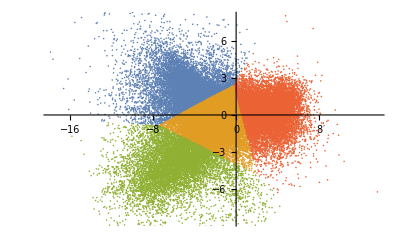

```mathematica
ListPlot[fctepexi]
```

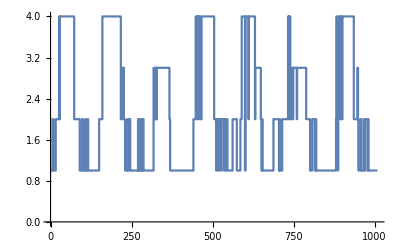

```mathematica
arrtepexi=ParallelTable[Count[fctepexi[[#]],tepexi[[j]]]&/@{1,2,3,4},{j,1,Length[tepexi]}];
markovtepexi=Table[Complement[{1,2,3,4},Flatten[Position[arrtepexi[[j]],0],1]][[1]],{j,1,Length[arrtepexi]}];
ListLinePlot[markovtepexi,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

```mathematica
estadostepexi= markovtepexi;

transtepexi= Table[{estadostepexi[[i]],estadostepexi[[i+1]]},{i,1,Length[estadostepexi]-1}];
Probtepexi[i_,j_]:=Length[Select[transtepexi,#=={i,j}&]]/Length[Select[transtepexi,#[[1]]==i&]] 
Mattepexi=Table[Probtepexi[i,j],{i,1,4},{j,1,4}]//MatrixForm
Mattepexi=Table[Probtepexi[i,j],{i,1,4},{j,1,4}]//MatrixForm // N
```

(19459/22963 | 1029/22963 | 1009/22963 | 1466/22963
972/11501 | 10378/11501 | 64/11501 | 87/11501
519/3962 | 27/7924 | 3389/3962 | 81/7924
1495/10098 | 67/10098 | 73/10098 | 2821/3366)

(0.847407 | 0.0448112 | 0.0439403 | 0.0638418
0.0845144 | 0.902356 | 0.00556473 | 0.00756456
0.130994 | 0.00340737 | 0.855376 | 0.0102221
0.148049 | 0.00663498 | 0.00722915 | 0.838087)

```mathematica
Export["estadostepexicompleto.csv",estadostepexi,"CSV"]
```

```mathematica
potenciatepexi1 = Total[0.6125(((fctepexi[[1]][[All,1]]^2+fctepexi[[1]][[All,2]]^2)^(1/2))^3)]/Length[fctepexi[[1]]]
potenciatepexi2 = Total[0.6125(((fctepexi[[2]][[All,1]]^2+fctepexi[[2]][[All,2]]^2)^(1/2))^3)]/Length[fctepexi[[2]]]
potenciatepexi3 = Total[0.6125(((fctepexi[[3]][[All,1]]^2+fctepexi[[3]][[All,2]]^2)^(1/2))^3)]/Length[fctepexi[[3]]]
potenciatepexi4 = Total[0.6125(((fctepexi[[4]][[All,1]]^2+fctepexi[[4]][[All,2]]^2)^(1/2))^3)]/Length[fctepexi[[4]]]
```

158.825

17.0399

330.732

42.154

San Fernando

```mathematica
plotsanfer = ListPlot[sanfer, AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, GridLines->{{0},{0}}, ColorFunction->LightPurple]
```

```mathematica
Histogram3D[sanfer,45,AxesOrigin->{-15,-20},AxesLabel->{"Vx [m/s]","Vy [m/s]"}, ColorFunction->"TemperatureMap"]
```

```mathematica
SmoothHistogram3D[sanfer, ColorFunction->"TemperatureMap",AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, PlotLegends->Automatic]
```

```mathematica
SmoothDensityHistogram[sanfer,ColorFunction->"SunsetColors"]
```

```mathematica
fcsanfer=FindClusters[sanfer,4,CriterionFunction->"CalinskiHarabasz"];
```

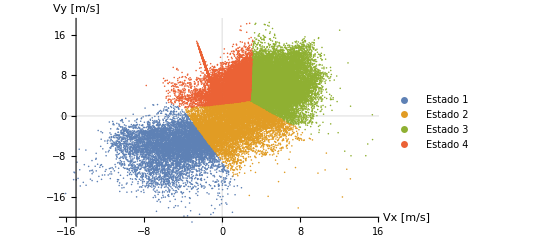

```mathematica
ListPlot[fcsanfer, PlotLegends->{"Estado 1", "Estado 2","Estado 3","Estado 4"},AxesLabel->{"Vx [m/s]","Vy [m/s]"}, AxesOrigin->{-15,-20}, GridLines->{{0},{0}}]
```

```mathematica
sanest1 = fcsanfer[[1]];
sanest2 = fcsanfer[[2]];
sanest3 = fcsanfer[[3]];
sanest4 = fcsanfer[[4]];
Length[sanest1]//N
Length[sanest2]//N
Length[sanest3]//N
Length[sanest4]//N
```

7962.

10104.

17987.

16468.

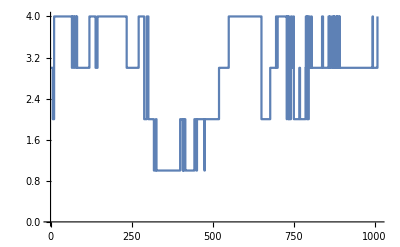

```mathematica
arrsanfer=ParallelTable[Count[fcsanfer[[#]],sanfer[[j]]]&/@{1,2,3,4},{j,1,Length[sanfer]}];
markovsanfer=Table[Complement[{1,2,3,4},Flatten[Position[arrsanfer[[j]],0],1]][[1]],{j,1,Length[arrsanfer]}];
ListLinePlot[markovsanfer,InterpolationOrder->0,AspectRatio->1/6,PlotTheme->"Detailed",FrameLabel->{"Tiempo [días]","Estado"},PlotStyle->{Orange, Thin},  ImageSize->Scaled[0.8]]
```

```mathematica
estadossanfer= markovsanfer;

transsanfer= Table[{estadossanfer[[i]],estadossanfer[[i+1]]},{i,1,Length[estadossanfer]-1}];
Probsanfer[i_,j_]:=Length[Select[transsanfer,#=={i,j}&]]/Length[Select[transsanfer,#[[1]]==i&]] ;
Matsanfer=Table[Probsanfer[i,j],{i,1,4},{j,1,4}]//MatrixForm
Matsanfer=Table[Probsanfer[i,j],{i,1,4},{j,1,4}]//MatrixForm // N
```

(8499/9266 | 121/4633 | 138/4633 | 249/9266
14/1331 | 17651/18634 | 3/18634 | 56/1331
299/7729 | 0 | 7425/7729 | 5/7729
273/16906 | 741/16906 | 12/8453 | 7934/8453)

(0.917224 | 0.026117 | 0.0297863 | 0.0268724
0.0105184 | 0.947247 | 0.000160996 | 0.0420736
0.0386855 | 0. | 0.960668 | 0.000646914
0.0161481 | 0.0438306 | 0.00141961 | 0.938602)

```mathematica
Export["estadossanfernandocompleto.csv",estadossanfer,"CSV"]
```

```mathematica
ventosadata= Import["..\\Data\\VENTOSALIMPIO_.csv"];
rumorosadata= Import["..\\Data\\RUMOROSALIMPIO_.csv"]; 
ojuelosdata = Import["..\\Data\\OJUELOSLIMPIO_.csv"];
tepexidata = Import["..\\Data\\TEPEXILIMPIO_.csv"];
sanferdata = Import["..\\Data\\SANFERNANDOLIMPIO_.csv"];
cuaudata = Import["..\\Data\\CUAHUTEMOCLIMPIO_.csv"];
meridadata = Import["..\\Data\\MERIDALIMPIO_.csv"];
```

```mathematica
{{meridadata}, {□}}
```

{{{{date,WS_80mA_mean,WD_78m_mean},{2018-01-01 00:00:00,5.6019,28.19},{2018-01-01 00:10:00,5.8562,27.09},{2018-01-01 00:20:00,5.8252,38.6},{2018-01-01 00:30:00,5.2174,45.29},{2018-01-01 00:40:00,3.9243,44.54},{2018-01-01 00:50:00,3.1552,76.93},{2018-01-01 01:00:00,3.8269,74.55},48042,{2018-12-31 22:50:00,8.4921,123.4},{2018-12-31 23:00:00,7.9649,122.7},{2018-12-31 23:10:00,7.2889,123.3},{2018-12-31 23:20:00,6.4826,123.5},{2018-12-31 23:30:00,6.3462,120.},{2018-12-31 23:40:00,6.5694,123.6},{2018-12-31 23:50:00,6.5074,122.3},{2019-01-01 00:00:00,7.3881,120.5}}},{□}}
 |  |  |  |

Mérida

```mathematica
stmerida1 = Table[{meridadata[[i,1]],estadosmerida[[i]]},{i,1,Length[estadosmerida]}];
dimerida1 = Table[{stmerida1[[i,1]],If[stmerida1[[i,2]]==1,1,0]},{i,1,Length[stmerida1]}]
timerida1 = Select[dimerida1,#[[2]]==1&]
```

{{date,0},{2018-01-01 00:00:00,0},{2018-01-01 00:10:00,0},{2018-01-01 00:20:00,0},{2018-01-01 00:30:00,0},{2018-01-01 00:40:00,1},{2018-01-01 00:50:00,0},{2018-01-01 01:00:00,0},{2018-01-01 01:10:00,0},{2018-01-01 01:20:00,1},{2018-01-01 01:30:00,1},{2018-01-01 01:40:00,1},{2018-01-01 01:50:00,1},52362,{2018-12-31 22:00:00,0},{2018-12-31 22:10:00,0},{2018-12-31 22:20:00,0},{2018-12-31 22:30:00,0},{2018-12-31 22:40:00,0},{2018-12-31 22:50:00,0},{2018-12-31 23:00:00,0},{2018-12-31 23:10:00,0},{2018-12-31 23:20:00,0},{2018-12-31 23:30:00,0},{2018-12-31 23:40:00,0},{2018-12-31 23:50:00,0}}
 |  |  |  |

{{2018-01-01 00:40:00,1},{2018-01-01 01:20:00,1},{2018-01-01 01:30:00,1},{2018-01-01 01:40:00,1},{2018-01-01 01:50:00,1},{2018-01-01 02:00:00,1},{2018-01-01 02:10:00,1},{2018-01-01 02:20:00,1},{2018-01-01 02:30:00,1},{2018-01-01 02:40:00,1},{2018-01-01 03:00:00,1},{2018-01-01 03:10:00,1},11567,{2018-12-31 00:00:00,1},{2018-12-31 00:50:00,1},{2018-12-31 04:50:00,1},{2018-12-31 05:20:00,1},{2018-12-31 13:20:00,1},{2018-12-31 13:30:00,1},{2018-12-31 13:40:00,1},{2018-12-31 13:50:00,1},{2018-12-31 15:00:00,1},{2018-12-31 15:10:00,1},{2018-12-31 15:20:00,1},{2018-12-31 16:20:00,1}}
 |  |  |  |

```mathematica
stmerida2 = Table[{meridadata[[i,1]],estadosmerida[[i]]},{i,1,Length[estadosmerida]}];
dimerida2 = Table[{stmerida2[[i,1]],If[stmerida2[[i,2]]==2,1,0]},{i,1,Length[stmerida2]}]
timerida2 = Select[dimerida2,#[[2]]==1&]
```

{{date,0},{2018-01-01 00:00:00,0},{2018-01-01 00:10:00,0},{2018-01-01 00:20:00,0},{2018-01-01 00:30:00,0},{2018-01-01 00:40:00,0},{2018-01-01 00:50:00,0},{2018-01-01 01:00:00,0},{2018-01-01 01:10:00,0},{2018-01-01 01:20:00,0},{2018-01-01 01:30:00,0},{2018-01-01 01:40:00,0},{2018-01-01 01:50:00,0},52362,{2018-12-31 22:00:00,0},{2018-12-31 22:10:00,0},{2018-12-31 22:20:00,0},{2018-12-31 22:30:00,0},{2018-12-31 22:40:00,0},{2018-12-31 22:50:00,0},{2018-12-31 23:00:00,0},{2018-12-31 23:10:00,0},{2018-12-31 23:20:00,0},{2018-12-31 23:30:00,0},{2018-12-31 23:40:00,0},{2018-12-31 23:50:00,0}}
 |  |  |  |

{{2018-01-02 06:50:00,1},{2018-01-03 03:30:00,1},{2018-01-03 07:40:00,1},{2018-01-03 07:50:00,1},{2018-01-03 08:00:00,1},{2018-01-03 08:10:00,1},{2018-01-03 08:20:00,1},{2018-01-03 08:30:00,1},{2018-01-03 08:40:00,1},{2018-01-03 08:50:00,1},{2018-01-03 09:00:00,1},{2018-01-03 09:10:00,1},4492,{2018-12-22 00:20:00,1},{2018-12-22 00:30:00,1},{2018-12-22 00:40:00,1},{2018-12-22 00:50:00,1},{2018-12-22 01:00:00,1},{2018-12-22 01:10:00,1},{2018-12-22 01:20:00,1},{2018-12-22 01:30:00,1},{2018-12-22 02:30:00,1},{2018-12-22 02:40:00,1},{2018-12-22 02:50:00,1},{2018-12-22 03:00:00,1}}
 |  |  |  |

```mathematica
stmerida3 = Table[{meridadata[[i,1]],estadosmerida[[i]]},{i,1,Length[estadosmerida]}];
dimerida3 = Table[{stmerida3[[i,1]],If[stmerida3[[i,2]]==3,1,0]},{i,1,Length[stmerida3]}]
timerida3 = Select[dimerida3,#[[2]]==1&]
```

{{date,0},{2018-01-01 00:00:00,0},{2018-01-01 00:10:00,0},{2018-01-01 00:20:00,0},{2018-01-01 00:30:00,0},{2018-01-01 00:40:00,0},{2018-01-01 00:50:00,0},{2018-01-01 01:00:00,0},{2018-01-01 01:10:00,0},{2018-01-01 01:20:00,0},{2018-01-01 01:30:00,0},{2018-01-01 01:40:00,0},{2018-01-01 01:50:00,0},52362,{2018-12-31 22:00:00,1},{2018-12-31 22:10:00,1},{2018-12-31 22:20:00,1},{2018-12-31 22:30:00,1},{2018-12-31 22:40:00,1},{2018-12-31 22:50:00,1},{2018-12-31 23:00:00,1},{2018-12-31 23:10:00,1},{2018-12-31 23:20:00,1},{2018-12-31 23:30:00,1},{2018-12-31 23:40:00,1},{2018-12-31 23:50:00,1}}
 |  |  |  |

{{2018-01-01 04:40:00,1},{2018-01-01 04:50:00,1},{2018-01-01 05:00:00,1},{2018-01-01 05:10:00,1},{2018-01-01 05:20:00,1},{2018-01-01 05:30:00,1},{2018-01-01 05:40:00,1},{2018-01-01 05:50:00,1},{2018-01-01 06:10:00,1},{2018-01-02 19:50:00,1},{2018-01-02 20:00:00,1},{2018-01-02 20:10:00,1},20167,{2018-12-31 22:00:00,1},{2018-12-31 22:10:00,1},{2018-12-31 22:20:00,1},{2018-12-31 22:30:00,1},{2018-12-31 22:40:00,1},{2018-12-31 22:50:00,1},{2018-12-31 23:00:00,1},{2018-12-31 23:10:00,1},{2018-12-31 23:20:00,1},{2018-12-31 23:30:00,1},{2018-12-31 23:40:00,1},{2018-12-31 23:50:00,1}}
 |  |  |  |

```mathematica
stmerida4 = Table[{meridadata[[i,1]],estadosmerida[[i]]},{i,1,Length[estadosmerida]}];
dimerida4 = Table[{stmerida4[[i,1]],If[stmerida4[[i,2]]==4,1,0]},{i,1,Length[stmerida4]}]
timerida4 = Select[dimerida4,#[[2]]==1&]
```

{{date,1},{2018-01-01 00:00:00,1},{2018-01-01 00:10:00,1},{2018-01-01 00:20:00,1},{2018-01-01 00:30:00,1},{2018-01-01 00:40:00,0},{2018-01-01 00:50:00,1},{2018-01-01 01:00:00,1},{2018-01-01 01:10:00,1},{2018-01-01 01:20:00,0},{2018-01-01 01:30:00,0},{2018-01-01 01:40:00,0},{2018-01-01 01:50:00,0},52362,{2018-12-31 22:00:00,0},{2018-12-31 22:10:00,0},{2018-12-31 22:20:00,0},{2018-12-31 22:30:00,0},{2018-12-31 22:40:00,0},{2018-12-31 22:50:00,0},{2018-12-31 23:00:00,0},{2018-12-31 23:10:00,0},{2018-12-31 23:20:00,0},{2018-12-31 23:30:00,0},{2018-12-31 23:40:00,0},{2018-12-31 23:50:00,0}}
 |  |  |  |

{{date,1},{2018-01-01 00:00:00,1},{2018-01-01 00:10:00,1},{2018-01-01 00:20:00,1},{2018-01-01 00:30:00,1},{2018-01-01 00:50:00,1},{2018-01-01 01:00:00,1},{2018-01-01 01:10:00,1},{2018-01-01 02:50:00,1},{2018-01-01 06:20:00,1},{2018-01-01 06:30:00,1},{2018-01-01 06:40:00,1},{2018-01-01 06:50:00,1},16064,{2018-12-30 15:50:00,1},{2018-12-30 16:00:00,1},{2018-12-30 16:10:00,1},{2018-12-30 16:20:00,1},{2018-12-30 16:30:00,1},{2018-12-30 16:40:00,1},{2018-12-30 16:50:00,1},{2018-12-30 17:00:00,1},{2018-12-30 17:10:00,1},{2018-12-30 17:20:00,1},{2018-12-30 17:30:00,1},{2018-12-30 18:00:00,1}}
 |  |  |  |

Ojuelos

```mathematica
stojuelos1= Table[{ojuelosdata[[i,1]],estadosojuelos[[i]]},{i,1,Length[estadosojuelos]}];
diojuelos1= Table[{stojuelos1[[i,1]],If[stojuelos1[[i,2]]==1,1,0]},{i,1,Length[stojuelos1]}]
tiojuelos1 = Select[diojuelos1,#[[2]]==1&]
```

```mathematica
stojuelos2 = Table[{ojuelosdata[[i,1]],estadosojuelos[[i]]},{i,1,Length[estadosojuelos]}];
diojuelos2 = Table[{stojuelos2[[i,1]],If[stojuelos2[[i,2]]==2,1,0]},{i,1,Length[stojuelos2]}]
tiojuelos2 = Select[diojuelos2,#[[2]]==1&]
```

```mathematica
stojuelos3= Table[{ojuelosdata[[i,1]],estadosojuelos[[i]]},{i,1,Length[estadosojuelos]}];
diojuelos3= Table[{stojuelos3[[i,1]],If[stojuelos3[[i,2]]==3,1,0]},{i,1,Length[stojuelos3]}]
tiojuelos3= Select[diojuelos3,#[[2]]==1&]
```

```mathematica
stojuelos4 = Table[{ojuelosdata[[i,1]],estadosojuelos[[i]]},{i,1,Length[estadosojuelos]}];
diojuelos4 = Table[{stojuelos4[[i,1]],If[stojuelos4[[i,2]]==4,1,0]},{i,1,Length[stojuelos4]}]
tiojuelos4 = Select[diojuelos4,#[[2]]==1&]
```

Rumorosa

```mathematica
strumorosa1 = Table[{rumorosadata[[i,1]],estadosrumorosa[[i]]},{i,1,Length[estadosrumorosa]}];
dirumorosa1 = Table[{strumorosa1[[i,1]],If[strumorosa1[[i,2]]==1,1,0]},{i,1,Length[strumorosa1]}]
tirumorosa1 = Select[dirumorosa1,#[[2]]==1&]
```

```mathematica
strumorosa2 = Table[{rumorosadata[[i,1]],estadosrumorosa[[i]]},{i,1,Length[estadosrumorosa]}];
dirumorosa2 = Table[{strumorosa2[[i,1]],If[strumorosa2[[i,2]]==2,1,0]},{i,1,Length[strumorosa2]}]
tirumorosa2 = Select[dirumorosa2,#[[2]]==1&]
```

```mathematica
strumorosa3 = Table[{rumorosadata[[i,1]],estadosrumorosa[[i]]},{i,1,Length[estadosrumorosa]}];
dirumorosa3 = Table[{strumorosa3[[i,1]],If[strumorosa3[[i,2]]==3,1,0]},{i,1,Length[strumorosa3]}]
tirumorosa3 = Select[dirumorosa3,#[[2]]==1&]
```

```mathematica
strumorosa4 = Table[{rumorosadata[[i,1]],estadosrumorosa[[i]]},{i,1,Length[estadosrumorosa]}];
dirumorosa4 = Table[{strumorosa4[[i,1]],If[strumorosa4[[i,2]]==4,1,0]},{i,1,Length[strumorosa4]}]
tirumorosa4 = Select[dirumorosa4,#[[2]]==1&]
```

Cuahutemoc

```mathematica
stcuau1 = Table[{cuaudata[[i,1]],estadoscuau[[i]]},{i,1,Length[estadoscuau]}];
dicuau1 = Table[{stcuau1[[i,1]],If[stcuau1[[i,2]]==1,1,0]},{i,1,Length[stcuau1]}]
ticuau1 = Select[dicuau1,#[[2]]==1&]
```

```mathematica
stcuau2 = Table[{cuaudata[[i,1]],estadoscuau[[i]]},{i,1,Length[estadoscuau]}];
dicuau2 = Table[{stcuau2[[i,1]],If[stcuau2[[i,2]]==2,1,0]},{i,1,Length[stcuau2]}]
ticuau2 = Select[dicuau2,#[[2]]==1&]
```

```mathematica
stcuau3 = Table[{cuaudata[[i,1]],estadoscuau[[i]]},{i,1,Length[estadoscuau]}];
dicuau3 = Table[{stcuau3[[i,1]],If[stcuau3[[i,2]]==3,1,0]},{i,1,Length[stcuau3]}]
ticuau3 = Select[dicuau3,#[[2]]==1&]
```

```mathematica
stcuau4 = Table[{cuaudata[[i,1]],estadoscuau[[i]]},{i,1,Length[estadoscuau]}];
dicuau4 = Table[{stcuau4[[i,1]],If[stcuau4[[i,2]]==4,1,0]},{i,1,Length[stcuau4]}]
ticuau4 = Select[dicuau4,#[[2]]==1&]
```

Tepexi

```mathematica
sttepexi1= Table[{tepexidata[[i,1]],estadostepexi[[i]]},{i,1,Length[estadostepexi]}];
ditepexi1 = Table[{sttepexi1[[i,1]],If[sttepexi1[[i,2]]==1,1,0]},{i,1,Length[sttepexi1]}]
titepexi1 = Select[ditepexi1,#[[2]]==1&]
```

```mathematica
sttepexi2= Table[{tepexidata[[i,1]],estadostepexi[[i]]},{i,1,Length[estadostepexi]}];
ditepexi2 = Table[{sttepexi2[[i,1]],If[sttepexi2[[i,2]]==2,1,0]},{i,1,Length[sttepexi2]}]
titepexi2 = Select[ditepexi2,#[[2]]==1&]
```

```mathematica
sttepexi3= Table[{tepexidata[[i,1]],estadostepexi[[i]]},{i,1,Length[estadostepexi]}];
ditepexi3= Table[{sttepexi3[[i,1]],If[sttepexi3[[i,2]]==3,1,0]},{i,1,Length[sttepexi3]}]
titepexi3 = Select[ditepexi3,#[[2]]==1&]
```

```mathematica
sttepexi4= Table[{tepexidata[[i,1]],estadostepexi[[i]]},{i,1,Length[estadostepexi]}];
ditepexi4 = Table[{sttepexi4[[i,1]],If[sttepexi4[[i,2]]==4,1,0]},{i,1,Length[sttepexi4]}]
titepexi4 = Select[ditepexi4,#[[2]]==1&]
```

Ventosa

```mathematica
stventosa= Table[{ventosadata[[i,1]],estadosventosa[[i]]},{i,1,Length[estadosventosa]}];
diventosa= Table[{stventosa[[i,1]],If[stventosa[[i,2]]==1,1,0]},{i,1,Length[stventosa]}]
tiventosa= Select[diventosa,#[[2]]==1&]
```

San Fernando

```mathematica
stsanfer1= Table[{sanferdata[[i,1]],estadossanfer[[i]]},{i,1,Length[estadossanfer]}];
disanfer1= Table[{stsanfer1[[i,1]],If[stsanfer1[[i,2]]==1,1,0]},{i,1,Length[stsanfer1]}]
tisanfer1 = Select[disanfer1,#[[2]]==1&]
```

```mathematica
stsanfer2= Table[{sanferdata[[i,1]],estadossanfer[[i]]},{i,1,Length[estadossanfer]}];
disanfer2= Table[{stsanfer2[[i,1]],If[stsanfer2[[i,2]]==2,1,0]},{i,1,Length[stsanfer2]}]
tisanfer2= Select[disanfer2,#[[2]]==1&]
```

```mathematica
stsanfer3= Table[{sanferdata[[i,1]],estadossanfer[[i]]},{i,1,Length[estadossanfer]}];
disanfer3= Table[{stsanfer3[[i,1]],If[stsanfer3[[i,2]]==3,1,0]},{i,1,Length[stsanfer3]}]
tisanfer3= Select[disanfer3,#[[2]]==1&]
```

```mathematica
stsanfer4= Table[{sanferdata[[i,1]],estadossanfer[[i]]},{i,1,Length[estadossanfer]}];
disanfer4= Table[{stsanfer4[[i,1]],If[stsanfer4[[i,2]]==4,1,0]},{i,1,Length[stsanfer4]}]
tisanfer4 = Select[disanfer4,#[[2]]==1&]
```

```mathematica
Export["rumorosaestado1.csv",dirumorosa1,"CSV"]
Export["rumorosaestado2.csv", dirumorosa2, "CSV"]
Export["rumorosaestado3.csv",dirumorosa3,"CSV"]
Export["rumorosaestado4.csv", dirumorosa4, "CSV"]

Export["meridaestado1.csv",dimerida1,"CSV"]
Export["meridaestado2.csv", dimerida2, "CSV"]
Export["meridaestado3.csv",dimerida3,"CSV"]
Export["meridaestado4.csv", dimerida4, "CSV"]

Export["ojuelosestado1.csv",diojuelos1,"CSV"]
Export["ojuelosestado2.csv", diojuelos2, "CSV"]
Export["ojuelosestado3.csv",diojuelos3,"CSV"]
Export["ojuelosestado4.csv", diojuelos4, "CSV"]

Export["cuauestado1.csv",dicuau1,"CSV"]
Export["cuauaestado2.csv", dicuau2, "CSV"]
Export["cuauestado3.csv",dicuau3,"CSV"]
Export["cuauaestado4.csv", dicuau4, "CSV"]

Export["sanferestado1.csv",disanfer1,"CSV"]
Export["sanferestado2.csv", disanfer2, "CSV"]
Export["sanferestado3.csv",disanfer3,"CSV"]
Export["sanferestado4.csv", disanfer4, "CSV"]

Export["tepexiestado1.csv",ditepexi1,"CSV"]
Export["tepexiestado2.csv", ditepexi2, "CSV"]
Export["tepexiestado3.csv",ditepexi3,"CSV"]
Export["tepexiestado4.csv", ditepexi4, "CSV"]

Export["ventosaestado1.csv",diventosa1,"CSV"]
Export["ventosaestado2.csv",diventosa2,"CSV"]
Export["ventosaestado3.csv",diventosa3,"CSV"]
Export["ventosaestado4.csv",diventosa4,"CSV"]
```

rumorosaestado4.csv